```mathematica
var[c1_,c2_,col_]:=Style[Subscript[Style[c1,Italic],c2],col];
```

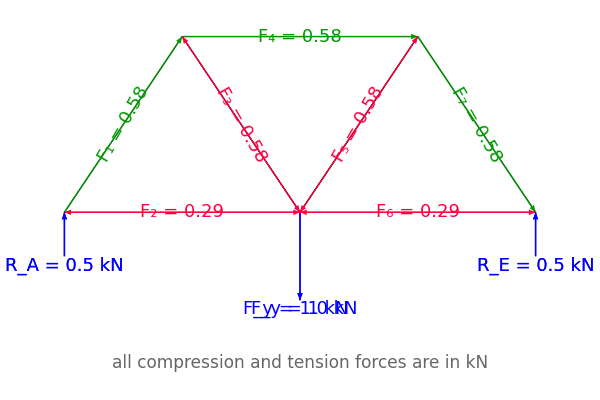

```mathematica
Module[{w,h,θ,Fy,sol,RA,RE,F1,F2,F3,F4,F5,F6,F7,colC,colT,colA},
w=1;h=w/2*Tan[θ];θ=60°;Fy=1;

(*sol=Quiet@Solve[N@{
(*reaction*)w*(-Fy)+2*w*re==0,ra+re-Fy==0,
(*A*)ra+f1*Sin[θ]==0,f1*Cos[θ]+f2==0,
(*B*)f1*Sin[θ]+f3*Sin[θ]==0,-f1*Cos[θ]+f3*Cos[θ]+f4==0,
(*C*)-Fy+f3*Sin[θ]+f5*Sin[θ]==0,-f2-f3*Cos[θ]+f5*Cos[θ]+f6==0,
(*D*)-f5*Sin[θ]-f7*Sin[θ]==0
},{ra,re,f1,f2,f3,f4,f5,f6,f7}][[1]];*)
sol=Quiet@Solve[N@{
(*reactions*)w*(-Fy)+2*w*re==0,ra+re-Fy==0,
(*A*)ra+f1*Sin[θ]==0,f1*Cos[θ]+f2==0,
(*B*)-f1*Sin[θ]-f3*Sin[θ]==0,-f1*Cos[θ]+f3*Cos[θ]+f4==0,
(*C*)f3*Sin[θ]+f5*Sin[θ]-Fy==0,-f2-f3*Cos[θ]+f5*Cos[θ]+f6==0,
(*D*)-f5*Sin[θ]-f7*Sin[θ]==0
},{ra,re,f1,f2,f3,f4,f5,f6,f7}][[1]];
(*sol=Quiet@Solve[N@{
(*reactions*)w*(-Fy)+2*w*re==0,ra+re-Fy==0,
(*A*)ra+f1*Sin[θ]==0,f1*Cos[θ]+f2==0,
(*B*)f1*Sin[θ]+f3*Sin[θ]==0,f1*Cos[θ]+f3*Cos[θ]+f4==0,
(*C*)f3*Sin[θ]+f5*Sin[θ]-Fy==0,f2+f3*Cos[θ]+f5*Cos[θ]+f6==0,
(*D*)f5*Sin[θ]+f7*Sin[θ]==0
},{ra,re,f1,f2,f3,f4,f5,f6,f7}][[1]];*)
RE=re/.sol;RA=ra/.sol;F1=f1/.sol;F2=f2/.sol;F3=f3/.sol;F4=f4/.sol;F5=f5/.sol;F6=f6/.sol;F7=f7/.sol;

colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];colA=RGBColor[0.55,0,1];

Graphics[{
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{0.5*w,h},{w,0}}],Polygon[{{0.5*w,h},{1.5*w,h},{w,0}}],Polygon[{{1.5*w,h},{2*w,0},{w,0}}]},

{Blue,Arrow[{{0,-0.25*h},{0,0}}],Arrow[{{w,0},{w,-0.5*h}}],Arrow[{{2*w,-0.25*h},{2*w,0}}],
Text[Style[Row@{var["F","y",Blue]," = ",Fy," kN"},18,Blue],{w,-0.5*h},{0,1.5}],
Text[Style[Row@{var["R",#1,Blue]," = ",#2," kN"},18,Blue],#3,{0,1.5}]&@@@{{"A",RA,{0,-0.25*h}},{"E",RE,{2*w,-0.25*h}}}},

{colC,Arrowheads@{{0.045,0.325},{-0.045,0.675}},Arrow[{{0,0},{0.5*w,h}}],Arrow[{{0.5*w,h},{1.5*w,h}}],Arrow[{{1.5*w,h},{2*w,0}}],
Text[Rotate[Style[Row@{var["F",#1,colC]," = ",NumberForm[Abs@#2,{4,2}]," "},18,Background->White],#4],#3]&@@@{
{1,F1,{w/4,h/2},θ},{4,F4,{w,h},0},{7,F7,{1.75*w,h/2},-θ}}},
{colT,Arrowheads@{-0.045,0.045},Arrow[{{0,0},{w,0}}],Arrow[{{w,0},{2*w,0}}],Arrow[{{0.5*w,h},{w,0}}],Arrow[{{w,0},{1.5*w,h}}],
Text[Rotate[Style[Row@{var["F",#1,colT]," = ",NumberForm[Abs@#2,{4,2}]," "},18,Background->White],#4],#3]&@@@{
{2,F2,{w/2,0},0},{3,F3,{0.75*w,h/2},-θ},{5,F5,{1.25*w,h/2},θ},{6,F6,{1.5*w,0},0}}},
{Blue,Arrow[{{0,-0.25*h},{0,0}}],Arrow[{{w,0},{w,-0.5*h}}],Arrow[{{2*w,-0.25*h},{2*w,0}}],
Text[Style[Row@{var["R",#1,Blue]," = ",NumberForm[N@#2,{3,1}]," kN"},18],#3,{0,1.5}]&@@@{{"A",RA,{0,-0.25*h}},{"E",RE,{2*w,-0.25*h}}},
Text[Style[Row@{var["F","y",Blue]," = ",NumberForm[N@Fy,{3,1}]," kN"},18],{w,-0.5*h},{0,1.5}]},
Text[Style[Row@{"all ",Style["compression",colC]," and ",Style["tension",colT]," forces are in kN"},17,GrayLevel@0.4],{w,-0.86*h}]
},ImageSize->{600,400}]
]
```